This notebook contains the functions used to create the energy landscapes in Figure 1 in the paper “Robust folding of elastic origami” and a shows how to create the ones in the figure. This notebook requires the mechanisms.m package, located at [ https://github.com/cdsantan/mechanisms ]. If there are version incompatibilities, please email marvlee@umass.edu or cdsantan@syr.edu for an older version.

```mathematica
<<"mechanisms`"
```

```mathematica
$mechanismsVersion
```

0.85

## Functions

### variablePattern[], indexPattern[], and expressionNumericQ[]

```mathematica
variablePattern=Except[_?NumericQ|_List];
indexPattern={ variablePattern, _?NumericQ, _?NumericQ};
```

```mathematica
expressionNumericQ[expression_,variables_]:=With[
{numericExpression=Flatten[{expression}/.Thread[variables->ConstantArray[0,Length[variables]]]]},
	NumericQ[numericExpression.numericExpression]
]
```

### findExtrema[]

#### wrapper

```mathematica
findExtrema::expr="Dimension of force does not match number of variables.";

toVectorField[expr_List,vars_]:=expr/;Length[expr]==Length[vars]
toVectorField[expr_List,vars_]:=(Message[findExtrema::expr]; $Failed)
toVectorField[expr_ : Except[_List], vars_]:=D[-expr,{vars}]
```

```mathematica
Options[findExtrema]={
	Method->Automatic
};

findExtrema[expression_, variables_, opt : OptionsPattern[]]:=
Module[{res=Switch[OptionValue[Method],
	Automatic,
		findExtremaInternalAutomatic[expression,variables],
	{"Solve",___}|"Solve",
		findExtremaInternalSolve[expression,variables,Sequence@@Rest[Flatten[{OptionValue[Method]}]]],
	{"NSolve",___}|"NSolve",
		findExtremaInternalNSolve[expression,variables,Sequence@@Rest[Flatten[{OptionValue[Method]}]]],
	{"FindRoot",___}|"FindRoot",
		findExtremaInternalFindRoot[expression,variables,Sequence@@Rest[Flatten[{OptionValue[Method]}]]]
]},
	res /; Head[res]===List
]
```

#### automatic

```mathematica
findExtremaInternalAutomatic[force_,variables : {variablePattern..}]:=findExtremaInternalNSolve[force,variables]/; expressionNumericQ[force,variables]
findExtremaInternalAutomatic[force_,variables : {variablePattern..}]:=findExtremaInternalSolve[force,variables]/; Not[expressionNumericQ[force,variables]]
findExtremaInternalAutomatic[force_,variables : {indexPattern..}]:=findExtremaInternalFindRoot[force,variables]

findExtrema::meth="Variables are not properly specified.";
findExtremaInternalAutomatic[_,_]:="nothing"/;Message[findExtrema::meth];
```

#### Solve[] version

```mathematica
Options[findExtremaInternalSolve]=Options[Solve];

findExtremaInternalSolve[expression_,variables : {variablePattern..}, opt : OptionsPattern[]]:=
With[{force=toVectorField[expression,variables]},
Module[
{solutions=Solve[force==0,variables,opt]},
	Transpose[{solutions,D[force,{variables}]/.solutions}] /; Head[solutions]=!=Solve
]]

findExtrema::solv="\"Solve\" method does not use variable bounds. Ignoring.";
findExtremaInternalSolve[force_,variables: {indexPattern..}, opt : OptionsPattern[]]:=(Message[findExtrema::solv]; findExtremaInternalSolve[force,variables[[All,1]],opt])
findExtremaInternalSolve[_,_,OptionsPattern[]]:="nothing"/;Message[findExtrema::var]
```

#### NSolve[] version

```mathematica
Options[findExtremaInternalNSolve]=Options[NSolve];

findExtremaInternalNSolve[expression_,variables : {variablePattern..}, opt : OptionsPattern[] ]:=
With[{force=toVectorField[expression,variables]},
Module[{solutions=NSolve[force==0,variables,Reals,opt]},
	If[Length[solutions]==0,{},Transpose[{solutions,D[force,{variables}]/.solutions}]] /; Head[solutions]=!=NSolve
]]

findExtrema::nsolv="\"NSolve\" method does not use variable bounds. Ignoring.";
findExtremaInternalNSolve[force_,variables : {indexPattern..}, opt : OptionsPattern[]]:=(Message[findExtrema::nsolv]; findExtremaInternalNSolve[force,variables[[All,1]],opt])
findExtremaInternalNSolve[_,_,OptionsPattern[]]:="nothing"/;Message[findExtrema::var]
```

#### FindRoot[] version

```mathematica
Options[findExtremaInternalFindRoot]=Join[
	{
		"InitialPoints"->50 (*# of initial linear points to use*),
		"RandomizeRange"->10^(-3) (* add a small random piece of this magnitude to each initial guess to avoid accidental symmetries *),
		ZeroTest->(#<10^(-12)&),
		SameTest->((#1-#2).(#1-#2)<10^(-8)&)
	},
	Options[FindRoot]
];

findExtremaInternalFindRoot[expression_, indices : {indexPattern..}, opt : OptionsPattern[]]:=
With[{ force=toVectorField[expression,indices[[All,1]]] },With[
{
	startingPoints=generateInitialPoints[force,OptionValue["InitialPoints"],OptionValue["RandomizeRange"],indices],
	maxValues=indices[[All,3]],
	minValues=indices[[All,2]],
	variables=indices[[All,1]],
	findrootOptions=Sequence@@FilterRules[{opt},Options[FindRoot]]
},
	outputResults[
		testResults[
			DeleteCases[
				Quiet[ FindRoot[force, #, findrootOptions]& /@ (Transpose[{variables,#,minValues,maxValues}]&/@startingPoints) ],
				_FindRoot
			],
			force,
			OptionValue[ZeroTest]
		],
		force,
		variables,
		OptionValue[SameTest]
	] /; startingPoints=!=$Failed
]]

findExtrema::ind="Method \"FindRoot\" needs to specify a range for each variable.";
findExtremaInternalFindRoot[expression_, indices : {variablePattern..}, opt : OptionsPattern[]]:="nothing"/;Message[findExtrema::ind]
```

```mathematica
generateInitialPoints[force_,numpoints_Integer?(#>0&),randomrange_?(NumericQ[#]&&#>0&),indices_]:=
With[
{
	gridPoints=Tuples[ Range[#[[1]],#[[2]],(#[[2]]-#[[1]])/numpoints]&/@indices[[ All,{2,3} ]] ]
},
	testInitialPoints[
		force,
		indices[[All,1]],
		10/numpoints,
		If[ randomrange==0, gridPoints, gridPoints + RandomReal[{-randomrange,randomrange},Dimensions[gridPoints]] ]
	]
]

generateInitialPoints[force_,pointlist_?(MatrixQ[#,NumericQ]&),randomrange_, indices_]:=pointlist /; Last[Dimensions[pointlist]]==Length[indices]

findExtrema::pl="Option \"InitialPoints\" is not a list of points with dimension equal to the number of indices.";
findExtrema::init="Option \"InitialPoints\" is not a positive integer or a list of points with dimension equal to the number of indices.";
findExtrema::init="Option \"RandomizeRange\" is not a positive number.";
generateInitialPoints[_,_Integer?(#>0&),_,_]:=(Message[findExtrema::rr]; $Failed)
generateInitialPoints[force_,pointlist_?(MatrixQ[#,NumericQ]&),randomrange_, indices_]:=(Message[findExtrema::pl]; $Failed)
generateInitialPoints[_,_,_,_]:=(Message[findExtrema::init]; $Failed)
```

```mathematica
testInitialPoints[vectorfield_,variables_,threshold_,points_]:=
	With[{mag=vectorfield . vectorfield},Select[points,(mag/.Thread[variables->#]) < threshold &]]
```

```mathematica
(*
Post-processing of the solutions from the multiple minimizations
*)

findExtrema::zerotest="ZeroTest function did not return Booleans on every solution. Outputting untested solutions.";

testResults[solutions_,force_,zerotestFunction_]:=
With[{tested=Map[zerotestFunction,force.force/.solutions]},
	If[AllTrue[tested,BooleanQ],
		Pick[solutions,tested],
		Message[findExtrema::zerotest];
		solutions
	]
]
testResults[{},_,_]:={}
testResults[solutions_,force_,None]:=solutions

(*eliminate duplicate solutions*)
outputResults[{},_,_,_]:={}

outputResults[solutions_,force_,variables_,Automatic]:=
With[{deletedSolutions=Thread[variables->#]&/@DeleteDuplicates[variables/.solutions]},
	Transpose[{deletedSolutions,D[force,{variables}]/.deletedSolutions}]
]/;Length[solutions]>0

outputResults[solutions_,force_,variables_,sametestFunction_]:=Module[
{deletedSolutions=Thread[variables->#]&/@DeleteDuplicates[variables/.solutions,sametestFunction]},
	Transpose[{deletedSolutions,D[force,{variables}]/.deletedSolutions}]
]/;Length[solutions]>0
```

## Origami Initialization

Start by setting up two versions of the birdsfoot: one with face folds and one without. The one without face folds will be used to create estimates.

```mathematica
six=changeCellData[_joint,"label"->"Index"]@singleVertex[{Pi/3,Pi/3,Pi/3,Pi/3,Pi/3,Pi/3}];
```

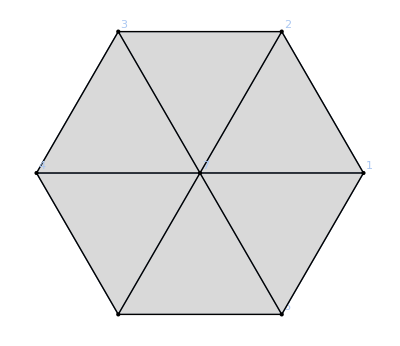

```mathematica
six2=addCells[six,{
fold[{7,2},{"angle"-> angles[1],"torsionalStiffness" -> k[1]}],
fold[{7,3},{"angle"-> angles[2],"torsionalStiffness" ->k[2]}],
fold[{7,4},{"angle"-> angles[3],"torsionalStiffness" ->k[3]}],
fold[{7,5},{"angle"-> angles[4],"torsionalStiffness" -> k[4]}],
fold[{7,6},{"angle"-> angles[5],"torsionalStiffness" ->k[5]}],
fold[{7,1},{"angle"-> angles[6],"torsionalStiffness" -> k[6]}]
}]
```

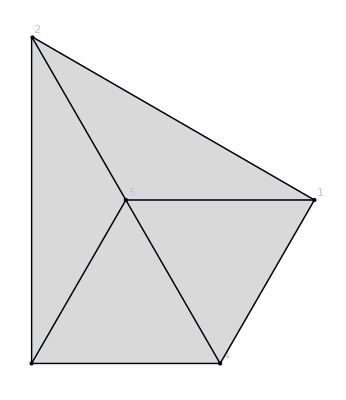

```mathematica
four=changeCellData[_joint,"label"->"Index"]@singleVertex[{Pi/3,2 Pi/3,2Pi/3,Pi/3}]
```

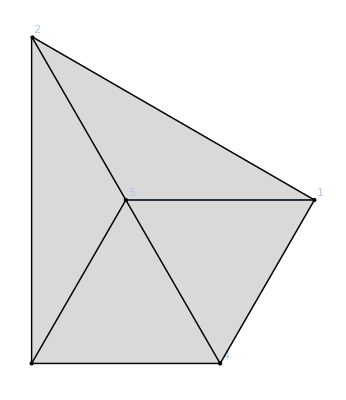

```mathematica
four2=addCells[four,{
fold[{5,1},{"torsionalStiffness"->k,"angle"->a[1]}],
fold[{5,2},{"torsionalStiffness"->k,"angle"->a[2]}],
fold[{5,3},{"torsionalStiffness"->k,"angle"->a[3]}],
fold[{5,4},{"torsionalStiffness"->k,"angle"->a[4]}]
}]
```

## Identify approximate extrema

Start by setting up the approximate stretching and torsion energy for the four fold origami, and use this energy to find the extrema. Since this is most accurate at the flat state, and all of the saddle points are almost at the flat state, we will use these saddle points as the points in the plot. For the minima, we will use the minima generated here as initial points for minimizing the interpolation functions created using the exact torsion and approximate stretching energy.

```mathematica
{linear,quadratic}=Simplify[infinitesimalMotions[four2,"constraints"->{vertexDisplacement[1,All[3]],vertexDisplacement[4,{"x","z"}],vertexDisplacement[5,"z"]},"variables"->{vertexDisplacement[2,"z"],vertexDisplacement[3,"z"]}]]
```

{{{0,0,0},{0,0,vertexDisplacement[2,z]},{0,0,vertexDisplacement[3,z]},{0,0,0},{0,0,0}},{(vertexDisplacement[2,z] (vertexDisplacement[2,z]+2 vertexDisplacement[3,z]))/(√22)}}

```mathematica
fullyApproximateEnergy=Module[{eps},(Normal@Series[((#.#&[DiagonalMatrix[Sqrt[Array[k,4]]] . (foldAngle[four2,vertexPosition[four2],{{5,1},{5,2},{5,3},{5,4}}]-Array[a,4])] )/.positionRules[four2["positions"]+{{0,0,0},{0,0,eps h2},{0,0,eps h3},{0,0,0},{0,0,0}}]) ,{eps,0,2}]/.eps->1)+ quadratic . quadratic/2/.{vertexDisplacement[2,"z"]->h2,vertexDisplacement[3,"z"]->h3}]
```

1/44 h2^2 (h2+2 h3)^2-(4 h2 a[1] k[1])/(√3)+a[1]^2 k[1]-4/3 (√3 h2+√3 h3) a[2] k[2]+a[2]^2 k[2]-(4 h2 a[3] k[3])/(√3)+a[3]^2 k[3]-(4 h3 a[4] k[4])/(√3)+a[4]^2 k[4]+4/3 (h2^2 k[1]+h2^2 k[2]+2 h2 h3 k[2]+h3^2 k[2]+h2^2 k[3]+h3^2 k[4])

Now initialize the fold stiffnesses and angles, noting that we have not accounted for the area of the faces in the linear springs, but these are just ball park estimates to give as seeds to find the true minima later. Note that all of the folds are unit length so the length dependence has been left implicit.

```mathematica
angles4=Thread[Array[a,4]->{0.01*i*(-mag),0.01*i*(-mag)+(1-0.01*i)*(mag),0.01*i*(-mag),0.01*i*(mag)+(1-0.01*i)*(mag)}]/.mag->(Pi/8)
```

{a[1]→-0.00392699 i,a[2]→-0.00392699 i+1/8 (1-0.01 i) π,a[3]→-0.00392699 i,a[4]→0.00392699 i+1/8 (1-0.01 i) π}

```mathematica
fourstiff=Thread[Array[k,4]->{10^(-4)/4,10^(-4)/4,10^(-4)/4,10^(-4)/4}]
```

{k[1]→1/40000,k[2]→1/40000,k[3]→1/40000,k[4]→1/40000}

Now lets find the extrema for the example landscapes in the paper.

```mathematica
fullenergy0=fullyApproximateEnergy/.fourstiff/.angles4/.i->0
```

7.71063×10^-6-0.0000226725 h3+1/44 h2^2 (h2+2 h3)^2-0.00001309 (√3 h2+√3 h3)+4/3 ((3 h2^2)/40000+(h2 h3)/20000+h3^2/20000)

```mathematica
extrema0=findExtrema[fullenergy0,{h2,h3}]
```

{{{h2→0.,h3→0.340087},{{-0.021229,-0.0000666667},{-0.0000666667,-0.000133333}}}}

```mathematica
fullenergy37=fullyApproximateEnergy/.fourstiff/.angles4/.i->37
```

5.17152×10^-6+0.0000167776 h2-0.0000226725 h3+1/44 h2^2 (h2+2 h3)^2-3.40339×10^-6 (√3 h2+√3 h3)+4/3 ((3 h2^2)/40000+(h2 h3)/20000+h3^2/20000)

```mathematica
extrema37=findExtrema[fullenergy37,{h2,h3}]
```

{{{h2→-0.00302916,h3→0.213122},{{-0.00810872,0.000165588},{0.000165588,-0.000135002}}},{{h2→-0.0580162,h3→0.0673375},{{0.000188516,0.000435972},{0.000435972,-0.000745312}}},{{h2→-0.142293,h3→0.0786354},{{-0.000743038,-0.00151984},{-0.00151984,-0.00381467}}}}

```mathematica
fullenergy44=fullyApproximateEnergy/.fourstiff/.angles4/.i->44
```

5.40361×10^-6+0.0000199518 h2-0.0000226725 h3+1/44 h2^2 (h2+2 h3)^2-1.5708×10^-6 (√3 h2+√3 h3)+4/3 ((3 h2^2)/40000+(h2 h3)/20000+h3^2/20000)

```mathematica
extrema44=findExtrema[fullenergy44,{h2,h3}]
```

{{{h2→-0.0046886,h3→0.18725},{{-0.00610215,0.00024659},{0.00024659,-0.00013733}}},{{h2→-0.043131,h3→0.0754141},{{0.0000327906,0.000608777},{0.000608777,-0.000471567}}},{{h2→-0.175831,h3→0.0923283},{{-0.00132669,-0.00259512},{-0.00259512,-0.00575453}}}}

```mathematica
fullenergy56=fullyApproximateEnergy/.fourstiff/.angles4/.i->56
```

6.32888×10^-6+0.0000253932 h2-0.0000226725 h3+1/44 h2^2 (h2+2 h3)^2+1.5708×10^-6 (√3 h2+√3 h3)+4/3 ((3 h2^2)/40000+(h2 h3)/20000+h3^2/20000)

```mathematica
extrema56=findExtrema[fullenergy56,{h2,h3}]
```

{{{h2→-0.0145396,h3→0.123424},{{-0.00204854,0.000528239},{0.000528239,-0.00017177}}},{{h2→-0.0185143,h3→0.111231},{{-0.0014197,0.000588704},{0.000588704,-0.000195657}}},{{h2→-0.227453,h3→0.115818},{{-0.0023794,-0.00459687},{-0.00459687,-0.0095397}}}}

```mathematica
fullenergy100=fullyApproximateEnergy/.fourstiff/.angles4/.i->100
```

0.0000154213+0.000045345 h2-0.0000226725 h3+1/44 h2^2 (h2+2 h3)^2+0.00001309 (√3 h2+√3 h3)+4/3 ((3 h2^2)/40000+(h2 h3)/20000+h3^2/20000)

```mathematica
extrema100=findExtrema[fullenergy100,{h2,h3}]
```

{{{h2→-0.408105,h3→0.204052},{{-0.00777044,-0.0152075},{-0.0152075,-0.0304151}}}}

## Interpolations

Now we need the full fold energy and approximate torsion energy for the version of the origami with face folds.

```mathematica
{linear6,quadratic6}=Simplify[infinitesimalMotions[six2,"constraints"->{vertexDisplacement[7,All[3]],vertexDisplacement[2,{"x","z"}],vertexDisplacement[1,"z"]},"variables"->vertexDisplacement[{3,4,5,6},"z"]]]
```

{{{0,0,0},{0,0,0},{0,0,vertexDisplacement[3,z]},{0,0,vertexDisplacement[4,z]},{0,0,vertexDisplacement[5,z]},{0,0,vertexDisplacement[6,z]},{0,0,0}},{-1/(2 √3)(vertexDisplacement[3,z]^2-2 vertexDisplacement[3,z] vertexDisplacement[4,z]+vertexDisplacement[4,z]^2-2 vertexDisplacement[4,z] vertexDisplacement[5,z]+(vertexDisplacement[5,z]-vertexDisplacement[6,z])^2)}}

```mathematica
pos=six2["positions"]+{{0,0,0},{0,0,0},{0,0,h3},{0,0,h4},{0,0,h5},{0,0,h6},{0,0,0}}
```

{{1,0,0},{1/2,(√3)/2,0},{-1/2,(√3)/2,h3},{-1,0,h4},{-1/2,-(√3)/2,h5},{1/2,-(√3)/2,h6},{0,0,0}}

```mathematica
approximateEnergy6=((#.#&[DiagonalMatrix[Sqrt[Array[k,6]]] . (foldAngle[six2,vertexPosition[six2],{{7,2},{7,3},{7,4},{7,5},{7,6},{7,1}}]-Array[a,6])] )/.positionRules[pos]) + quadratic6 . quadratic6/2/.{vertexDisplacement[3,"z"]->h3,vertexDisplacement[4,"z"]->h4,vertexDisplacement[5,"z"]->h5,vertexDisplacement[6,"z"]->h6}
```

1/24 (h3^2-2 h3 h4+h4^2-2 h4 h5+(h5-h6)^2)^2+(-a[1]+ArcTan[3/4,(√3 h3)/2])^2 k[1]+(-a[2]+ArcTan[3/4+1/2 h3 (h3-h4/2)+(3 h3 h4)/4,√(1+h3^2) (-(√3 h3)/2+(√3 h4)/2)])^2 k[2]+(-a[3]+ArcTan[3/4+(3 h4^2)/4+(h3-h4/2) (h4/2-h5),√(1+h4^2) ((√3 h3)/2-(√3 h4)/2+(√3 h5)/2)])^2 k[3]+(-a[4]+ArcTan[3/4+(h4/2-h5) (-h5/2-h6/2)+1/2 √3 h4 ((√3 h5)/2-(√3 h6)/2),√(1+h5^2) ((√3 h4)/4-(√3 h5)/2-1/2 √3 (-h4/2-h6))])^2 k[4]+(-a[5]+ArcTan[3/4-(-h5/2-h6/2) h6,((√3 h5)/2-(√3 h6)/2) √(1+h6^2)])^2 k[5]+(-a[6]+ArcTan[3/4,(√3 h6)/2])^2 k[6]

Now define the stiffnesses, with the face folds a factor of 100 stiffer than the active folds. This is simply for example purposes.

```mathematica
sixstiff=Thread[Array[k,6]->{10^(-4)/4,100*10^(-4)/4,10^(-4)/4,100*10^(-4)/4,10^(-4)/4,10^(-4)/4}]
```

{k[1]→1/40000,k[2]→1/400,k[3]→1/40000,k[4]→1/400,k[5]→1/40000,k[6]→1/40000}

And set up the derivatives for the interpolation functions and the function to create the data for the interpolations:

```mathematica
dE=D[approximateEnergy6,{{h4,h6}}];
```

```mathematica
dE2=D[approximateEnergy6,{{h4,h6},2}];
```

```mathematica
energyData[f_,g_,i_]:=Module[
{target=Thread[Array[a,6]->{0.01*i*(-Pi/8),0,0.01*i*(-Pi/8)+(1-0.01*i)*(Pi/8),0,0.01*i*(-Pi/8),0.01*i*(Pi/8)+(1-0.01*i)*(Pi/8)}],
workingEn,funcValue},
workingEn=approximateEnergy6/.target/.sixstiff/.h4->f/.h6->g;
funcValue=FindMinimum[workingEn,{h3,h5},MaxIterations->10^6];
{{f,g},funcValue[[1]],dE/.target/.sixstiff/.funcValue[[2]]/.h4->f/.h6->g,dE2/.target/.sixstiff/.funcValue[[2]]/.h4->f/.h6->g}
]
```

Now generate the data for the 5 energy landscapes seen in Fig. 1, create the interpolation, and find the minima.

```mathematica
data0=Flatten[Table[energyData[x,y,0],{x,-0.5,0.5,0.01},{y,-0.5,0.5,0.01}],1]
```

{{{-0.5,-0.5},0.00175481,{-0.00339419,-0.00166667},{{0.00203892,0.0154305},{0.0154305,0.0631912}}},10199,{{0.5,0.5},0.000842804,{0.000481071,22},{{1.13094,0.295936},{0.295936,0.0781554}}}}
 |  |  |  |

```mathematica
inter0=Quiet[Interpolation[data0]]
```

InterpolatingFunction[…]

```mathematica
extrema0
```

{{{h2→0.,h3→0.340087},{{-0.021229,-0.0000666667},{-0.0000666667,-0.000133333}}}}

```mathematica
p0min=FindMinimum[{inter0[h4,h6],-0.5<h4<0.5&&-0.5<h6<0.5},{{h4,0},{h6,0.3401}}]
```

{1.16803×10^-7,{h4→-6.1581×10^-6,h6→0.313504}}

```mathematica
data37=Flatten[Table[energyData[x,y,37],{x,-0.5,0.5,0.01},{y,-0.5,0.5,0.01}],1]
```

{{{-0.5,-0.5},0.00175146,{-0.00339241,-0.00166865},{{0.00314925,0.0188892},{0.0188892,0.0692839}}},10199,{{0.5,0.5},0.000872128,{0.000501091,22},{{1.12287,0.291018},{0.291018,0.0761538}}}}
 |  |  |  |

```mathematica
inter37=Quiet[Interpolation[data37]]
```

InterpolatingFunction[…]

```mathematica
extrema37
```

{{{h2→-0.00302916,h3→0.213122},{{-0.00810872,0.000165588},{0.000165588,-0.000135002}}},{{h2→-0.0580162,h3→0.0673375},{{0.000188516,0.000435972},{0.000435972,-0.000745312}}},{{h2→-0.142293,h3→0.0786354},{{-0.000743038,-0.00151984},{-0.00151984,-0.00381467}}}}

```mathematica
p37min1=FindMinimum[{inter37[h4,h6],-0.5<h4<0.5&&-0.5<h6<0.5},{{h4,-0.00302916},{h6,0.21312}}]
```

{2.08185×10^-6,{h4→-0.0011676,h6→0.201105}}

```mathematica
p37min2=FindMinimum[{inter37[h4,h6],-0.5<h4<0.5&&-0.5<h6<0.5},{{h4,-0.142293},{h6,0.0786354}}]
```

{3.21402×10^-6,{h4→-0.140224,h6→0.0735405}}

```mathematica
data44=Flatten[Table[energyData[x,y,44],{x,-0.5,0.5,0.01},{y,-0.5,0.5,0.01}],1]
```

{{{-0.5,-0.5},0.000881932,{-0.000484175,-0.00072624},{{1.12595,0.2929},{0.2929,0.0768792}}},10199,{{0.5,0.5},0.000878378,{0.000504895,22},{{1.12134,0.290093},{0.290093,0.0757797}}}}
 |  |  |  |

```mathematica
inter44=Quiet[Interpolation[data44]]
```

InterpolatingFunction[…]

```mathematica
extrema44
```

{{{h2→-0.0046886,h3→0.18725},{{-0.00610215,0.00024659},{0.00024659,-0.00013733}}},{{h2→-0.043131,h3→0.0754141},{{0.0000327906,0.000608777},{0.000608777,-0.000471567}}},{{h2→-0.175831,h3→0.0923283},{{-0.00132669,-0.00259512},{-0.00259512,-0.00575453}}}}

```mathematica
p44min1=FindMinimum[{inter44[h4,h6],-0.5<h4<0.5&&-0.5<h6<0.5},{{h4,-0.0046886},{h6,0.18725}}]
```

{2.92052×10^-6,{h4→-0.00164409,h6→0.18096}}

```mathematica
p44min2=FindMinimum[{inter44[h4,h6],-0.5<h4<0.5&&-0.5<h6<0.5},{{h4,-0.175831},{h6,0.0923283}}]
```

{2.67624×10^-6,{h4→-0.169864,h6→0.0880789}}

```mathematica
data56=Flatten[Table[energyData[x,y,56],{x,-0.5,0.5,0.01},{y,-0.5,0.5,0.01}],1]
```

{{{-0.5,-0.5},0.000872522,{-0.000477691,-0.000722071},{{1.12857,0.294497},{0.294497,0.0775294}}},10199,{{0.5,0.5},0.000889612,{0.000511427,22},{{1.11873,0.288513},{0.288513,0.0751418}}}}
 |  |  |  |

```mathematica
inter56=Quiet[Interpolation[data56]]
```

InterpolatingFunction[…]

```mathematica
extrema56
```

{{{h2→-0.0145396,h3→0.123424},{{-0.00204854,0.000528239},{0.000528239,-0.00017177}}},{{h2→-0.0185143,h3→0.111231},{{-0.0014197,0.000588704},{0.000588704,-0.000195657}}},{{h2→-0.227453,h3→0.115818},{{-0.0023794,-0.00459687},{-0.00459687,-0.0095397}}}}

```mathematica
p56min1=FindMinimum[{inter56[h4,h6],-0.5<h4<0.5&&-0.5<h6<0.5},{{h4,-0.0145396},{h6,0.123424}}]
```

{4.69764×10^-6,{h4→-0.00283943,h6→0.160724}}

```mathematica
p56min2=FindMinimum[{inter56[h4,h6],-0.5<h4<0.5&&-0.5<h6<0.5},{{h4,-0.227453},{h6,0.115818}}]
```

{1.94784×10^-6,{h4→-0.220471,h6→0.111145}}

```mathematica
data100=Flatten[Table[energyData[x,y,100],{x,-0.5,0.5,0.01},{y,-0.5,0.5,0.01}],1]
```

{{{-0.5,-0.5},0.000843632,{-0.000454042,-0.000706846},{{1.1382,0.300404},{0.300404,0.0799511}}},10199,{{0.5,0.5},0.000936416,{0.000535508,22},{{1.10918,0.282768},{0.282768,0.072838}}}}
 |  |  |  |

```mathematica
inter100=Quiet[Interpolation[data100]]
```

InterpolatingFunction[…]

```mathematica
extrema100
```

{{{h2→-0.408105,h3→0.204052},{{-0.00777044,-0.0152075},{-0.0152075,-0.0304151}}}}

```mathematica
p100min=FindMinimum[{inter100[h4,h6],-0.5<h4<0.5&&-0.5<h6<0.5},{{h4,-0.408105},{h6,0.204052}}]
```

{2.31051×10^-6,{h4→-0.323633,h6→0.161642}}

## Plots

Now to actually create the plots and place the extrema on the plots. We’d also like to show the target fold angles, although that is for a highly deformed mechanism. We can take advantage of the fact that f and h are linearly related by f=Mh to quadratic order where M is a matrix, and use the linearization with the heights from the minima at the end points as the endpoints:

```mathematica
{h4mid,h6mid}={(1-0.01*i)*(h4/.p0min[[2,1]])+0.01*i*(h4/.p100min[[2,1]]),(1-0.01*i)*(h6/.p0min[[2,2]])+0.01*i*(h6/.p100min[[2,2]])}
```

{-6.1581×10^-6 (1-0.01 i)-0.00323633 i,0.313504 (1-0.01 i)+0.00161642 i}

```mathematica
line=Line[{{h4mid,h6mid}/.i->0,{h4mid,h6mid}/.i->37,{h4mid,h6mid}/.i->56,{h4mid,h6mid}/.i->100}];
```

Then we also need to write a function to process the data above into a form that can be used in ListContourPlot[]:

```mathematica
proc[list_]:=Table[Flatten[{list[[i,1]],list[[i,2]]}],{i,1,Length[list]}]
```

Now we can put all of our pieces together:

```mathematica
m0=Point[{h4,h6}/.p0min[[2]]]
```

Point[{-6.1581×10^-6,0.313504}]

```mathematica
targ0=Point[{h4mid,h6mid}/.i->0]
```

Point[{-6.1581×10^-6,0.313504}]

```mathematica
endata0=proc[data0];
```

```mathematica
land0=ListContourPlot[endata0,Contours->10^(Range[-6,-3.5,0.25]),ColorFunction->(ColorData["LakeColors"][Rescale[#,{0,0.0004}]]&),ColorFunctionScaling->False,PlotLegends->Automatic,FrameLabel->{"h4","h6"},FrameStyle->Directive[Black,14],LabelStyle->{Black,FontSize->14}];
```

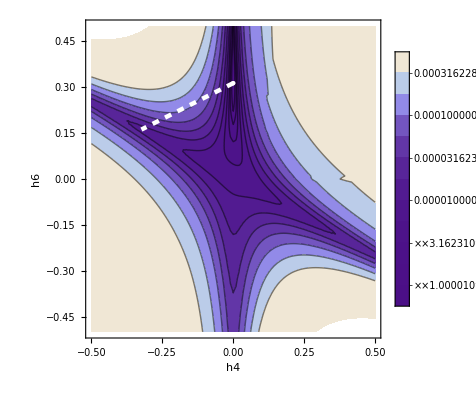

```mathematica
Show[land0,Graphics[{Dashed,Thickness[0.008],White,line}],Graphics[{PointSize[Large],White,targ0}],Graphics[{PointSize[Large],White,m0}]]
```

```mathematica
m371=Point[{h4,h6}/.p37min1[[2]]]
```

Point[{-0.0011676,0.201105}]

```mathematica
m372=Point[{h4,h6}/.p37min2[[2]]]
```

Point[{-0.140224,0.0735405}]

```mathematica
s37=Point[{h2,h3}/.extrema37[[2,1]]]
```

Point[{-0.0580162,0.0673375}]

```mathematica
targ37=Point[{h4mid,h6mid}/.i->37]
```

Point[{-0.119748,0.257315}]

```mathematica
endata37=proc[data37];
```

```mathematica
land37=ListContourPlot[endata37,Contours->10^(Range[-6,-3.5,0.25]),ColorFunction->(ColorData["LakeColors"][Rescale[#,{0,0.0004}]]&),ColorFunctionScaling->False,PlotLegends->Automatic,FrameLabel->{"h4","h6"},FrameStyle->Directive[Black,14],LabelStyle->{Black,FontSize->14}];
```

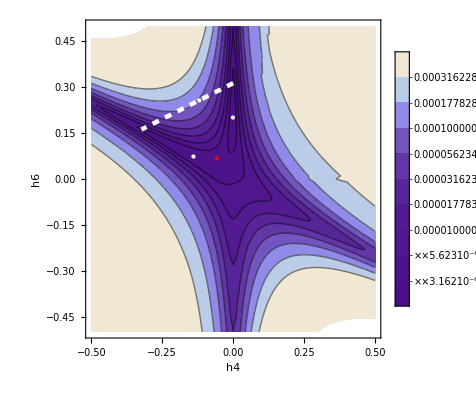

```mathematica
Show[land37,Graphics[{Dashed,Thickness[0.008],White,line}],Graphics[{PointSize[Large],White,targ37}],Graphics[{PointSize[Large],White,m371}],Graphics[{PointSize[Large],White,m372}],Graphics[{PointSize[Large],Red,s37}]]
```

```mathematica
m441=Point[{h4,h6}/.p44min1[[2]]]
```

Point[{-0.00164409,0.18096}]

```mathematica
m442=Point[{h4,h6}/.p44min2[[2]]]
```

Point[{-0.169864,0.0880789}]

```mathematica
s44=Point[{h2,h3}/.extrema44[[2,1]]]
```

Point[{-0.043131,0.0754141}]

```mathematica
targ44=Point[{h4mid,h6mid}/.i->44]
```

Point[{-0.142402,0.246684}]

```mathematica
endata44=proc[data44];
```

```mathematica
land44=ListContourPlot[endata44,Contours->10^(Range[-6,-3.5,0.25]),ColorFunction->(ColorData["LakeColors"][Rescale[#,{0,0.0004}]]&),ColorFunctionScaling->False,PlotLegends->Automatic,FrameLabel->{"h4","h6"},FrameStyle->Directive[Black,14],LabelStyle->{Black,FontSize->14}];
```

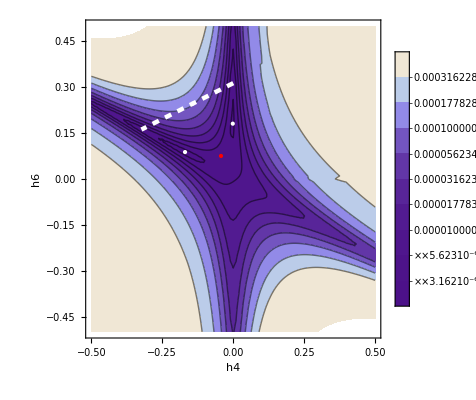

```mathematica
Show[land44,Graphics[{Dashed,Thickness[0.008],White,line}],Graphics[{PointSize[Large],White,targ44}],Graphics[{PointSize[Large],White,m441}],Graphics[{PointSize[Large],White,m442}],Graphics[{PointSize[Large],Red,s44}]]
```

```mathematica
m561=Point[{h4,h6}/.p56min1[[2]]]
```

Point[{-0.00283943,0.160724}]

```mathematica
m562=Point[{h4,h6}/.p56min2[[2]]]
```

Point[{-0.220471,0.111145}]

```mathematica
s56=Point[{h2,h3}/.extrema56[[2,1]]]
```

Point[{-0.0185143,0.111231}]

```mathematica
targ56=Point[{h4mid,h6mid}/.i->56]
```

Point[{-0.181237,0.228461}]

```mathematica
endata56=proc[data56];
```

```mathematica
land56=ListContourPlot[endata56,Contours->10^(Range[-6,-3.5,0.25]),ColorFunction->(ColorData["LakeColors"][Rescale[#,{0,0.0004}]]&),ColorFunctionScaling->False,PlotLegends->Automatic,FrameLabel->{"h4","h6"},FrameStyle->Directive[Black,14],LabelStyle->{Black,FontSize->14}];
```

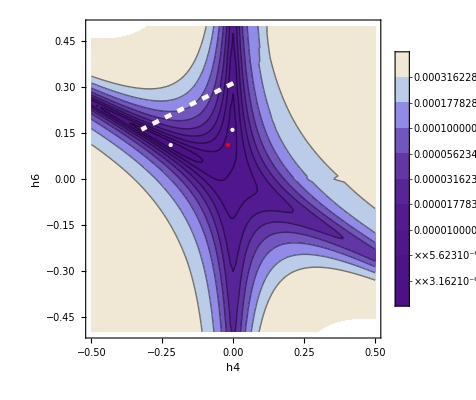

```mathematica
Show[land56,Graphics[{Dashed,Thickness[0.008],White,line}],Graphics[{PointSize[Large],White,targ56}],Graphics[{PointSize[Large],White,m561}],Graphics[{PointSize[Large],White,m562}],Graphics[{PointSize[Large],Red,s56}]]
```

```mathematica
m100=Point[{h4,h6}/.p100min[[2]]]
```

Point[{-0.323633,0.161642}]

```mathematica
targ100=Point[{h4mid,h6mid}/.i->100]
```

Point[{-0.323633,0.161642}]

```mathematica
endata100=proc[data100];
```

```mathematica
land100=ListContourPlot[endata100,Contours->10^(Range[-6,-3.5,0.25]),ColorFunction->(ColorData["LakeColors"][Rescale[#,{0,0.0004}]]&),ColorFunctionScaling->False,PlotLegends->Automatic,FrameLabel->{"h4","h6"},FrameStyle->Directive[Black,14],LabelStyle->{Black,FontSize->14}];
```

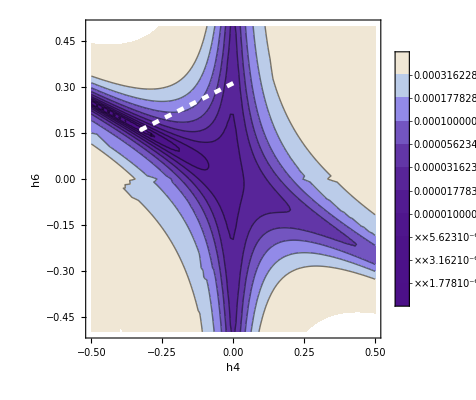

```mathematica
Show[land100,Graphics[{Dashed,Thickness[0.008],White,line}],Graphics[{PointSize[Large],White,targ100}],Graphics[{PointSize[Large],White,m100}]]
```